# Derivation of Accelerated Bi-Maxwellian differential number flux including loss cone physics

### Assumptions

```mathematica
Clear[E0pa,E0pe]
as=#>0&/@{E0pa,E0pe,E0,me,neS,neI,U0,δ,ϵ,u0};
as=Join[as,{β>1}];
```

```mathematica
E0pa=E0;
E0pe=E0;
```

### At the plasma sheet, we start with a bi-Maxwellian

```mathematica
gd3vS=neS(me/(2π))^(3/2)1/(E0pa^(1/2)E0pe)Exp[-(me vpa^2/2)/E0pa-(me vpe^2/2)/E0pe]vpe dvpa dvpe dϕ;(*bi-Maxwellian at source *)
Integrate[gd3vS/(dvpa dvpe dϕ),{vpa,-∞,∞},{vpe,0,∞},{ϕ,0,2π},Assumptions->as]
```

neS

### With no collisions, the electrons velocities will only change in two ways: 1) The perpendicular speed will increase as the B field converges, i.e. mirror force 2) The parallel electric potential change will increase the square magnitude of the speed by 2U_0/m_e

```mathematica
vpeS=1/Sqrt[β] vpeI(*conservation of first adiabatic invariant*)
vpaS=FullSimplify[Solve[vpaI^2+vpeI^2==vvpaS^2+vpeS^2+(2U0)/me,vvpaS][[2,1,2]],Assumptions->as](*conservation of energy*)
```

vpeI/(√β)

√(-(2 U0)/me+vpaI^2+(vpeI^2 (-1+β))/β)

### By Liouville’s theorem: f(v_(||,M),v_(⊥,M))=f(v_(||,I),v_(⊥,I))

```mathematica
(*no need for determinant. Doing a change of variables on any differential always works. need for no theorem then*)
```

```mathematica
gd2vI=FullSimplify[(2π)/dϕ gd3vS/.{vpe->vpeS,vpa->vpaS},Assumptions->as](*integrate over ϕ*)
FullSimplify[neS (me^(3/2)/Sqrt[2π])/(E0pa^(1/2)E0pe)Exp[-(me(vpaI^2+vpeI^2(β-1)/β-(2U0)/me))/(2E0pa)-(me vpeI^2/β)/(2E0pe)] vpeI/Sqrt[β] dvpa dvpe/ gd2vI,Assumptions->as]
```

(dvpa dvpe ⅇ^((2 U0-me (vpaI^2+vpeI^2)+((-E0pa+E0pe) me vpeI^2)/(E0pe β))/(2 E0pa)) me^(3/2) neS vpeI)/(E0pe √(2 π) √(E0pa β))

1

```mathematica
neI==FullSimplify[Integrate[gd2vI/(dvpa dvpe),{vpaI,-∞,∞},{vpeI,0,∞},Assumptions->as],Assumptions->as]
```

neI==(ⅇ^(U0/E0pa) E0pa neS √β)/(E0pa+E0pe (-1+β))

### Now that we have f_I(v_(||),v_⊥)dv_(||)dv_⊥dϕ, we determine the parallel differential number flux

```mathematica
Jpad2vI=FullSimplify[vpaI gd2vI,Assumptions->as]
```

(dvpa dvpe ⅇ^((2 U0-me (vpaI^2+vpeI^2)+((-E0pa+E0pe) me vpeI^2)/(E0pe β))/(2 E0pa)) me^(3/2) neS vpaI vpeI)/(E0pe √(2 π) √(E0pa β))

### Changing coordinates from (v_(||),v_⊥) to (v,θ) to (E,θ)

```mathematica
vpa2Eθ=Sqrt[(2EE)/me]Cos[θ];(*v_(||) = v cos(θ), v = √(2E/Subscript[m, e])*)
vpe2Eθ=Sqrt[(2EE)/me]Sin[θ];(*v_⊥ = v sin(θ), v = √(2E/Subscript[m, e])*)
J=FullSimplify[{{D[vpa2Eθ,EE],D[vpa2Eθ,θ]},{D[vpe2Eθ,EE],D[vpe2Eθ,θ]}},Assumptions->as];
DetJ=FullSimplify[Det[J],Assumptions->as]
```

1/me

```mathematica
Jpad2EI=FullSimplify[Jpad2vI/.{vpeI->vpe2Eθ,vpaI->vpa2Eθ}/.{dvpa dvpe->DetJ dE dθ},Assumptions->as]
FullSimplify[neS/Sqrt[2π me] 1/(E0pa^(1/2)E0pe)Sin[2θ]/Sqrt[β] EE Exp[-(EE-U0)/E0pa-(EE/E0pe-EE/E0pa)Sin[θ]^2/β]dE dθ/Jpad2EI,Assumptions->as]
```

(dE dθ ⅇ^((-E0pa EE+E0pe (EE-2 EE β+2 U0 β)+(E0pa-E0pe) EE Cos[2 θ])/(2 E0pa E0pe β)) EE neS Sin[2 θ])/(E0pe √(2 π) √(E0pa me β))

1

### Plotting J_(||)(E,θ)

```mathematica
plt=FullSimplify[(Jpad2EI E0pa^(1/2)me^(1/2)neS^-1)/(dE dθ)Exp[-u0]/.{E0pe->δ E0pa,EE->ϵ E0pa,U0->u0 E0pa},Assumptions->as]
Manipulate[
Plot3D[
plt/.{β->1000,δ->δδ}
,{ϵ,0,10}
,{θ,0,π}
,Ticks->{Automatic,{0,π/4,π/2,3π/4,π},Automatic}
,PlotRange->{{0,10},All,{-1,1}10^-2}
,AxesLabel->{"E/E_(0,  ||)","θ [rad]","J_(||) E_(0,  ||) m_e^(1/2) n_e^-1"}
,ImageSize->Large
]
,{{δδ,2},0.1,10}
]
```

(ⅇ^(-(ϵ (1+(-1+2 β) δ+(-1+δ) Cos[2 θ]))/(2 β δ)) ϵ Sin[2 θ])/(√(2 π) √β δ)

```mathematica
ββ=10;
polarplt=plt/.{ϵ->Sqrt[ϵpa^2+ϵpe^2],θ->ArcTan[ϵpa,Abs[ϵpe]]}/.{β->ββ}
plts=Table[
ContourPlot[
polarplt/.{δ->δδ}
,{ϵpa,0,5}
,{ϵpe,-5,5}
,Frame->True
,FrameStyle->Directive[Black,20]
,FrameLabel->{{"ϵ_⊥",""},{"ϵ_(||)","δ="<>ToString[δδ]}}
,ImageSize->450
,Contours->8
,PlotLegends->BarLegend[Automatic,LegendLabel->"e^(-SubscriptBox[u, 0])j_(||)(ϵ,θ)",LabelStyle->{Black,20}]
,ColorFunction->"Rainbow"
,AspectRatio->1
]
,{δδ,{0.1,0.5,1,2,5,10}}
];
pltgrid=GraphicsGrid[Partition[plts,3],Spacings->0,ImageSize->1800]
Export[NotebookDirectory[]<>"fluxes_beta="<>ToString[ββ]<>".png",pltgrid]
```

(ⅇ^(-(√(ϵpa^2+ϵpe^2) (1+19 δ+(-1+δ) Cos[2 ArcTan[ϵpa,Abs[ϵpe]]]))/(20 δ)) √(ϵpa^2+ϵpe^2) Sin[2 ArcTan[ϵpa,Abs[ϵpe]]])/(2 √(5 π) δ)

-Graphics-

D:\Files\research\thesis\notebooks\fluxes_beta=10.png

### Integrate over all azimuths and v_(||)>0, i.e. 0≤ θ≤ π/2

```mathematica
JpadEI=FullSimplify[Integrate[Jpad2EI/dθ,{θ,0,π/2},Assumptions->as],Assumptions->as]
```

(dE ⅇ^((-EE+U0)/E0pa-EE/(E0pe β)) (-ⅇ^(EE/(E0pa β))+ⅇ^(EE/(E0pe β))) E0pa neS β)/((E0pa-E0pe) √(2 π) √(E0pa me β))

### Recast in cleaner parameters

```mathematica
G[x_]:=(Exp[x]-1)/x
Limit[G[x],x->0]
JpadϵI=FullSimplify[JpadEI/.{EE->ϵ E0pa,U0->u0 E0pa,E0pe->δ E0pa,dE->dϵ E0pa},Assumptions->as]
FullSimplify[neS Sqrt[E0pa/(2π me)] 1/(δ Sqrt[β]) G[(δ-1)/(β δ)ϵ]ϵ Exp[-ϵ+u0]dϵ/JpadϵI,Assumptions->as]
```

1

(dϵ ⅇ^(u0-ϵ) (-1+ⅇ^(((-1+δ) ϵ)/(β δ))) E0pa neS β)/(√(2 π) √(E0pa me β) (-1+δ))

1

### Approximate for β Δ→∞

```mathematica
Series[G[x],{x,0,1}]
```

1+x/2+O[x]^2

```mathematica
dJpaapprox=neS Sqrt[E0pa/(2π me)] 1/(δ Sqrt[β]) (1+(δ-1)/(2β δ)ϵ)ϵ Exp[-ϵ+u0]dϵ;
```

### Re-normalize for Q_0

```mathematica
ne2q0={neS->Solve[q0==Integrate[ϵ dJpaapprox/dϵ,{ϵ,u0,∞},Assumptions->as],neS][[1,1,2]]};
dJpa=FullSimplify[dJpaapprox/.ne2q0,Assumptions->as]
```

(dϵ ⅇ^(u0-ϵ) q0 ϵ (2 β δ+(-1+δ) ϵ))/(-u0 (6+u0 (3+u0))+6 (-1+δ)+(4 β+u0 (6+4 β+u0 (3+u0+2 β))) δ)

```mathematica
dJpaχ=FullSimplify[dJpa/.β->(δ-1)/(2δ χ),Assumptions->as]
```

(dϵ ⅇ^(u0-ϵ) q0 ϵ (1+ϵ χ))/(2+6 χ+u0 (2+u0+(6+u0 (3+u0)) χ))

### Sanity checks

```mathematica
ne2Q0=neS->Solve[Q0==Integrate[EE Limit[JpadEI/dE,E0pe->E0pa],{EE,U0,∞},Assumptions->as],neS][[1,1,2]];
dJpaGEMINI=FullSimplify[Limit[JpadEI,E0pe->E0pa]/.ne2Q0,Assumptions->as]
FullSimplify[Q0/(E0pa^2+(E0pa+U0)^2)EE/E0pa Exp[-(EE-U0)/E0pa]dE/dJpaGEMINI,Assumptions->as]
```

(dE ⅇ^((-EE+U0)/E0pa) EE Q0)/(E0pa (2 E0pa^2+2 E0pa U0+U0^2))

1

```mathematica
Limit[dJpa,δ->1]/.{u0->U0/E0pa,ϵ->EE/E0pa,dϵ->dE/E0pa,q0->Q0/E0pa}//FullSimplify
Limit[dJpa,δ->1]/.{u0->0,ϵ->EE/E0pa,dϵ->dE/E0pa,q0->Q0/E0pa}//FullSimplify
```

(dE ⅇ^((-EE+U0)/E0pa) EE Q0)/(E0pa (2 E0pa^2+2 E0pa U0+U0^2))

(dE ⅇ^(-EE/E0pa) EE Q0)/(2 E0pa^3)

### Plotting differential number fluxes

```mathematica
mw=Limit[dJpa/(dϵ q0),δ->1]/.u0->0
MW=mw/.ϵ->EE/E0pa/.E0pa->1
```

(ⅇ^-ϵ ϵ)/2

(ⅇ^-EE EE)/2

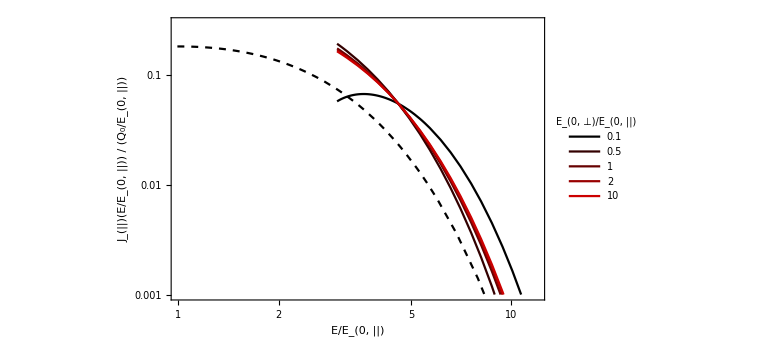

D:\Files\research\thesis\notebooks\dJpa_beta=10.png

```mathematica
βs=10;
δs={0.1,0.5,1,2,10};
plts=Table[dJpa/(dϵ q0)/.{u0->3,β->βs},{δ,δs}];
plt=Show[
LogLogPlot[
plts
,{ϵ,3,100}
,Frame->True
,FrameStyle->Directive[Black,20]
,FrameLabel->{{"J_(||)(E/E_(0,  ||)) / (Q_0/E_(0,  ||))",""},{"E/E_(0,  ||)","u_0 = 3,  β = "<>ToString[βs]}}
,ImageSize->Large
,PlotRange->{{1,12},{10^-3,0.3}}
,PlotStyle->(RGBColor[{#,0,0}]&/@(Range[0,Length[plts]]/Length[plts]))
,PlotLegends->LineLegend[δs,LegendLabel->"E_(0,  ⊥)/E_(0,  ||)"]
,GridLines->{{3},Automatic}
]
,LogLogPlot[
mw
,{ϵ,0.1,100}
,PlotStyle->{Black,Dashed}
]
]
Export[NotebookDirectory[]<>"dJpa_beta="<>ToString[βs]<>".png",plt]
```

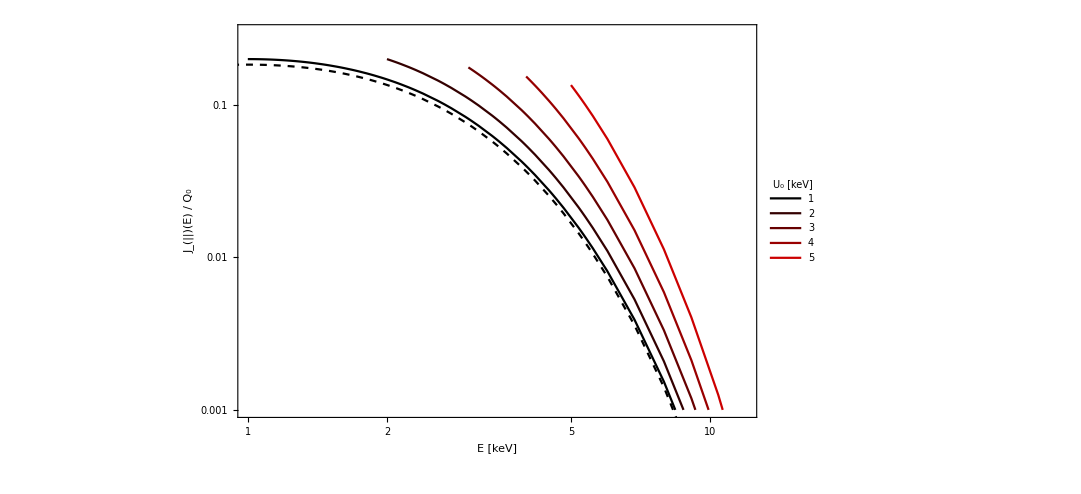

D:\Files\research\thesis\notebooks\dJpaGEMINI.png

```mathematica
U0s={1,2,3,4,5};
plts=Table[Piecewise[{{dJpaGEMINI/(dE Q0),EE≥U0}}]/.E0pa->1,{U0,U0s}];
plt=Show[
LogLogPlot[
plts
,{EE,0.1,100}
,Frame->True
,FrameStyle->Directive[Black,20]
,FrameLabel->{{"J_(||)(E) / Q_0",""},{"E [keV]","E_(0,  ||) = 1 keV"}}
,ImageSize->800
,PlotRange->{{1,12},{10^-3,0.3}}
,PlotStyle->(RGBColor[{#,0,0}]&/@(Range[0,Length[plts]]/Length[plts]))
,PlotLegends->LineLegend[U0s,LegendLabel->"U_0 [keV]"]
,GridLines->{U0s,Automatic}
]
,LogLogPlot[
MW
,{EE,0.1,100}
,PlotStyle->{Black,Dashed}
]
]
Export[NotebookDirectory[]<>"dJpaGEMINI.png",plt]
```

```mathematica
FullSimplify[Limit[Jpad2EI,E0pe->E0pa]/.ne2Q0/.E0pa->E0,Assumptions->as]
```

(dE dθ ⅇ^((-EE+U0)/E0) EE Q0 Sin[2 θ])/(E0 (2 E0^2+2 E0 U0+U0^2))

```mathematica
U0s0=Join[{0},U0s];
imgs=Table[
aaa=FullSimplify[Limit[Jpad2EI,E0pe->E0pa]/.ne2Q0/.E0pa->E0,Assumptions->as];
plts=Table[(aaa E0^2)/(dE dθ Q0)/.E0->1,{U0,U0s0}]/.{EE->Sqrt[Epa^2+Epe^2],θ->ArcTan[Epa,Abs[Epe]]};
ContourPlot[
plts[[i]]
,{Epa,0,8}
,{Epe,-8,8}
,Frame->True
,FrameStyle->Directive[Black,20]
,FrameLabel->{{"E_⊥ [keV]",""},{"E_(||) [keV]","E_0 = 1 keV,  U_0 = "<>ToString[U0s0[[i]]]<>" keV"}}
,ImageSize->450
,Contours->10
,PlotRange->{0,0.2}
,PlotLegends->BarLegend[Automatic,LegendLabel->"J_(||)(E,θ)E_0^2/Q_0",LabelStyle->{Black,20}]
,ColorFunction->"Rainbow"
,AspectRatio->1
,Epilog->{White,Disk[{0,0},{1,1}U0s0[[i]],{-π/2,π/2}],Black,Circle[{0,0},{1,1}U0s0[[i]],{-π/2,π/2}]}
]
,{i,1,Length[U0s0]}];
plt=GraphicsGrid[Partition[imgs,3],Spacings->0,ImageSize->1800]
Export[NotebookDirectory[]<>"butterflies.png",plt]
```

-Graphics-

D:\Files\research\thesis\notebooks\butterflies.png

```mathematica
Integrate[Sin[θ],{θ,0,π/4}]2//N
```

0.585786